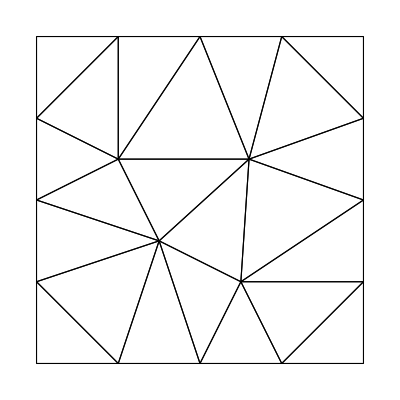

```mathematica
region=Rectangle[{0,0},{1,1}];
Needs["NDSolve`FEM`"];
h=0.1; 
(*Generate triangular mesh*)
em=ToElementMesh[region,"MeshOrder"->1,"MeshElementType"->"TriangleElement",MaxCellMeasure->h];

(*Extract mesh elements and nodes*)
elements=em["MeshElements"][[1,1]];
nodes=em["Coordinates"];

(*Compute triangle centroids for labeling*)
(*centroids=Mean[nodes[[#]]]&/@elements;*)

(*Create text labels for each triangle*)
(*labels=MapThread[Text[Style[#1,12,Blue],#2]&,{Range[Length[elements]],centroids}];*)

(*Show mesh with labeled triangle indices*)
Show[em["Wireframe"](*,Graphics[labels]*)]
```

```mathematica
(*UNIT TESTING*)
compareMatricies[M1_,M2_]:= Total[Abs[M2-M1],Length[Dimensions[M1]]]>10^-14
(*M0*)
(*Test for element 1*)
dots=nodes[[elements[[1]]]];
If[dots≠{{0.625,0.25},{0.5,0.},{0.75,0.}},Print["ERROR IN DOTS!"]]
{a,b,c}=Inverse[{{1,dots[[1,1]],dots[[1,2]]},
{1,dots[[2,1]],dots[[2,2]]},
{1,dots[[3,1]],dots[[3,2]]}}];
If[a≠{0,3,-2},Print["ERROR IN a!"]]
If[b≠{0,-4,4},Print["ERROR IN b!"]]
If[c≠{4,-2,-2},Print["ERROR IN c!"]]
triangle=Triangle[dots];
M=Table[Integrate[(a[[j]]+b[[j]]*x+c[[j]]*y)*(a[[k]]+b[[k]]*x+c[[k]]*y),{x,y}∈triangle],{k,1,3},{j,1,3}];
Print[M];
Print[calculateLocalM0[dots]]
```

{{0.00520833,0.00260417,0.00260417},{0.00260417,0.00520833,0.00260417},{0.00260417,0.00260417,0.00520833}}

{{0.00520833,0.00260417,0.00260417},{0.00260417,0.00520833,0.00260417},{0.00260417,0.00260417,0.00520833}}

```mathematica
(*Test for all elements*)
For[i=1,i≤Length[elements],i++,
dots=nodes[[elements[[i]]]];
{a,b,c}=Inverse[{{1,dots[[1,1]],dots[[1,2]]},
{1,dots[[2,1]],dots[[2,2]]},
{1,dots[[3,1]],dots[[3,2]]}}];
triangle=Triangle[dots];
M=Table[Integrate[(a[[j]]+b[[j]]*x+c[[j]]*y)*(a[[k]]+b[[k]]*x+c[[k]]*y),{x,y}∈triangle],{j,1,3},{k,1,3}];
precM0=calculateLocalM0[dots];
If[compareMatricies[M,precM0],Print["ERROR IN ELEMENT"]]
]
```

```mathematica
(*Test for Dα*)
For[i=1,i≤Length[elements],i++,
dots=nodes[[elements[[i]]]];
{a,b,c}=Inverse[{{1,dots[[1,1]],dots[[1,2]]},
{1,dots[[2,1]],dots[[2,2]]},
{1,dots[[3,1]],dots[[3,2]]}}];
triangle=Triangle[dots];
Dx=Table[Integrate[(a[[j]]+b[[j]]*x+c[[j]]*y)*D[(a[[k]]+b[[k]]*x+c[[k]]*y),x],{x,y}∈triangle],{j,1,3},{k,1,3}];
Dy=Table[Integrate[(a[[j]]+b[[j]]*x+c[[j]]*y)*D[(a[[k]]+b[[k]]*x+c[[k]]*y),y],{x,y}∈triangle],{j,1,3},{k,1,3}];
If[compareMatricies[{Dx,Dy},calculateLocalDα[dots]],Print["ERROR IN ELEMENT"]]
]
```

```mathematica
(*Test for R on τi*)
For[i=1,i≤6,i++,
dots=nodes[[elements[[i]]]];
{a,b,c}=Inverse[{{1,dots[[1,1]],dots[[1,2]]},
{1,dots[[2,1]],dots[[2,2]]},
{1,dots[[3,1]],dots[[3,2]]}}];
For[j=1,j≤3,j++,
allNodes={1,2,3};
allNodes = DeleteCases[allNodes,j];
     lineSegment[t_]:=(1-t) dots[[allNodes[[1]]]]+t dots[[allNodes[[2]]]];
     R=Table[Integrate[(#[[1]]*b[[k]]+#[[2]]*c[[k]]+a[[k]])*(#[[1]]*b[[s]]+#[[2]]*c[[s]]+a[[s]])&@lineSegment[t]*Norm[D[lineSegment[t],t]],{t,0,1}],{k,1,3},{s,1,3}];
precR=calculateLocalR[dots,j];
     If[compareMatricies[R,precR],Print["ERROR IN ELEMENT"]]
];

]
```

```mathematica
(*Test for R on τk*)
neighbours = tri2Tri[nodes,elements];
For[i=1,i≤6,i++,
dots=nodes[[elements[[i]]]];
For[j=1,j≤3,j++,
k=neighbours[[i,j]];
If[k==-1,Continue[]];
dots=nodes[[elements[[k]]]];
{a,b,c}=Inverse[{{1,dots[[1,1]],dots[[1,2]]},
{1,dots[[2,1]],dots[[2,2]]},
{1,dots[[3,1]],dots[[3,2]]}}];
kSide=-1;
For[s=1,s≤3,s++,
If[neighbours[[k,s]]==i,kSide=s]
];
If[kSide==-1,Print["ERROR IN CALCULATING SIDE INDICES"]];
allNodes={1,2,3};
allNodes = DeleteCases[allNodes,kSide];
     lineSegment[t_]:=(1-t) dots[[allNodes[[1]]]]+t dots[[allNodes[[2]]]];
     R=Table[Integrate[(#[[1]]*b[[k]]+#[[2]]*c[[k]]+a[[k]])*(#[[1]]*b[[s]]+#[[2]]*c[[s]]+a[[s]])&@lineSegment[t]*Norm[D[lineSegment[t],t]],{t,0,1}],{k,1,3},{s,1,3}];
     If[compareMatricies[R,calculateLocalR[dots,kSide]],Print["ERROR IN ELEMENT"]]
];
]
```

```mathematica
(*Test for normal vector*)
For[i=1,i≤6,i++,
dots=nodes[[elements[[i]]]];
For[j=1,j≤3,j++,
allNodes={1,2,3};
allNodes=DeleteCases[allNodes,j];
n=getNormalVectorOfJthSide[dots,j];
If[n[[1]]^2+n[[2]]^2<1.,Print["ERROR IN CALCULATING NORMAL VECTORS size"]; Print[n[[1]]^2+n[[2]]^2]];
If[n.dots[[allNodes[[1]]]]-dots[[allNodes[[2]]]]≠0.,Print["ERROR IN CALCULATING NORMAL VECTORS direction"];Print[n.{allNodes[[1]],allNodes[[2]]}]];
If[EuclideanDistance[dots[[allNodes[[1]]]]+n,dots[[j]]]< EuclideanDistance[dots[[allNodes[[1]]]]-n,dots[[j]]],
Print["ERROR IN CALCULATING NORMAL VECTORS side"];Print[EuclideanDistance[dots[[allNodes[[1]]]]+n,dots[[j]]]];
Print[EuclideanDistance[dots[[allNodes[[1]]]]-n,dots[[j]]]]
];
]
]
```

```mathematica
(*Test KroneckerProduct and PlanarAngle*)
A={{1,2},{3,4}};
B={{0,2},{7,0.5}};
KroneckerProduct[A,B]
KroneckerProduct[B,A]
PlanarAngle[{{-1,0},{0,0},{1,-1}}]
```

{{0.,2.,0.,4.},{7.,0.5,14.,1.},{0.,6.,0.,8.},{21.,1.5,28.,2.}}

{{0.,0.,2.,4.},{0.,0.,6.,8.},{7.,14.,0.5,1.},{21.,28.,1.5,2.}}

```mathematica
(*local matricies*)
p={1-x-y, x,y};
(*Dx,Dy*)
Table[Integrate[p[[i]]*D[p[[j]],x], {x,0, 1}, {y, 0, 1-x}], {i,1,3}, {j,1,3}]
Table[Integrate[p[[i]]*D[p[[j]],y], {x,0, 1}, {y, 0, 1-x}], {i,1,3}, {j,1,3}]
(*R*)
f={0,x,1-x};
Table[Integrate[f[[i]]*f[[j]],{x,0,1}], {i,1,3},{j,1,3}]
(*M0*)
Table[Integrate[p[[i]]*p[[j]], {x,0, 1}, {y, 0, 1-x}], {i,1,3}, {j,1,3}]
(*An ги имам на хартия*)
```

{{-1/6,1/6,0},{-1/6,1/6,0},{-1/6,1/6,0}}

{{-1/6,0,1/6},{-1/6,0,1/6},{-1/6,0,1/6}}

{{0,0,0},{0,1/3,1/6},{0,1/6,1/3}}

{{1/12,1/24,1/24},{1/24,1/12,1/24},{1/24,1/24,1/12}}